```mathematica
(*problem:solve x''[t]+w^2*x[t]=0 by using series apprimation and compare with teh exact solution.The initial conditions are x[0]=1,x'[0]=0*)
```

```mathematica
deq=x''[t]+w^2*x[t]==0;
initial={x[0]==1,x'[0]==0};
s=100;
ser=x[t]+O[t]^s
```

x[0]+x'[0] t+1/2 x''[0] t^2+1/6 x^(3)[0] t^3+1/24 x^(4)[0] t^4+1/120 x^(5)[0] t^5+1/720 x^(6)[0] t^6+(x^(7)[0] t^7)/5040+(x^(8)[0] t^8)/40320+(x^(9)[0] t^9)/362880+(x^(10)[0] t^10)/3628800+(x^(11)[0] t^11)/39916800+(x^(12)[0] t^12)/479001600+(x^(13)[0] t^13)/6227020800+(x^(14)[0] t^14)/87178291200+(x^(15)[0] t^15)/1307674368000+(x^(16)[0] t^16)/20922789888000+(x^(17)[0] t^17)/355687428096000+(x^(18)[0] t^18)/6402373705728000+(x^(19)[0] t^19)/121645100408832000+(x^(20)[0] t^20)/2432902008176640000+(x^(21)[0] t^21)/51090942171709440000+(x^(22)[0] t^22)/1124000727777607680000+(x^(23)[0] t^23)/25852016738884976640000+(x^(24)[0] t^24)/620448401733239439360000+(x^(25)[0] t^25)/15511210043330985984000000+(x^(26)[0] t^26)/403291461126605635584000000+(x^(27)[0] t^27)/10888869450418352160768000000+(x^(28)[0] t^28)/304888344611713860501504000000+(x^(29)[0] t^29)/8841761993739701954543616000000+(x^(30)[0] t^30)/265252859812191058636308480000000+(x^(31)[0] t^31)/8222838654177922817725562880000000+(x^(32)[0] t^32)/263130836933693530167218012160000000+(x^(33)[0] t^33)/8683317618811886495518194401280000000+(x^(34)[0] t^34)/295232799039604140847618609643520000000+(x^(35)[0] t^35)/10333147966386144929666651337523200000000+(x^(36)[0] t^36)/371993326789901217467999448150835200000000+(x^(37)[0] t^37)/13763753091226345046315979581580902400000000+(x^(38)[0] t^38)/523022617466601111760007224100074291200000000+(x^(39)[0] t^39)/20397882081197443358640281739902897356800000000+(x^(40)[0] t^40)/815915283247897734345611269596115894272000000000+(x^(41)[0] t^41)/33452526613163807108170062053440751665152000000000+(x^(42)[0] t^42)/1405006117752879898543142606244511569936384000000000+(x^(43)[0] t^43)/60415263063373835637355132068513997507264512000000000+(x^(44)[0] t^44)/2658271574788448768043625811014615890319638528000000000+(x^(45)[0] t^45)/119622220865480194561963161495657715064383733760000000000+(x^(46)[0] t^46)/5502622159812088949850305428800254892961651752960000000000+(x^(47)[0] t^47)/258623241511168180642964355153611979969197632389120000000000+(x^(48)[0] t^48)/12413915592536072670862289047373375038521486354677760000000000+(x^(49)[0] t^49)/608281864034267560872252163321295376887552831379210240000000000+(x^(50)[0] t^50)/30414093201713378043612608166064768844377641568960512000000000000+(x^(51)[0] t^51)/1551118753287382280224243016469303211063259720016986112000000000000+(x^(52)[0] t^52)/80658175170943878571660636856403766975289505440883277824000000000000+(x^(53)[0] t^53)/4274883284060025564298013753389399649690343788366813724672000000000000+(x^(54)[0] t^54)/230843697339241380472092742683027581083278564571807941132288000000000000+(x^(55)[0] t^55)/12696403353658275925965100847566516959580321051449436762275840000000000000+(x^(56)[0] t^56)/710998587804863451854045647463724949736497978881168458687447040000000000000+(x^(57)[0] t^57)/40526919504877216755680601905432322134980384796226602145184481280000000000000+(x^(58)[0] t^58)/2350561331282878571829474910515074683828862318181142924420699914240000000000000+(x^(59)[0] t^59)/138683118545689835737939019720389406345902876772687432540821294940160000000000000+(x^(60)[0] t^60)/8320987112741390144276341183223364380754172606361245952449277696409600000000000000+(x^(61)[0] t^61)/507580213877224798800856812176625227226004528988036003099405939480985600000000000000+(x^(62)[0] t^62)/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+(x^(63)[0] t^63)/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000+(x^(64)[0] t^64)/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000+(x^(65)[0] t^65)/8247650592082470666723170306785496252186258551345437492922123134388955774976000000000000000+(x^(66)[0] t^66)/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+(x^(67)[0] t^67)/36471110918188685288249859096605464427167635314049524593701628500267962436943872000000000000000+(x^(68)[0] t^68)/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000+(x^(69)[0] t^69)/171122452428141311372468338881272839092270544893520369393648040923257279754140647424000000000000000+(x^(70)[0] t^70)/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+(x^(71)[0] t^71)/850478588567862317521167644239926010288584608120796235886430763388588680378079017697280000000000000000+(x^(72)[0] t^72)/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000+(x^(73)[0] t^73)/4470115461512684340891257138125051110076800700282905015819080092370422104067183317016903680000000000000000+(x^(74)[0] t^74)/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+(x^(75)[0] t^75)/24809140811395398091946477116594033660926243886570122837795894512655842677572867409443815424000000000000000000+(x^(76)[0] t^76)/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000+(x^(77)[0] t^77)/145183092028285869634070784086308284983740379224208358846781574688061991349156420080065207861248000000000000000000+(x^(78)[0] t^78)/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+(x^(79)[0] t^79)/894618213078297528685144171539831652069808216779571907213868063227837990693501860533361810841010176000000000000000000+(x^(80)[0] t^80)/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000+(x^(81)[0] t^81)/5797126020747367985879734231578109105412357244731625958745865049716390179693892056256184534249745940480000000000000000000+(x^(82)[0] t^82)/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+(x^(83)[0] t^83)/39455239697206586511897471180120610571436503407643446275224357528369751562996629334879591940103770870906880000000000000000000+(x^(84)[0] t^84)/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000+(x^(85)[0] t^85)/281710411438055027694947944226061159480056634330574206405101912752560026159795933451040286452340924018275123200000000000000000000+(x^(86)[0] t^86)/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+(x^(87)[0] t^87)/2107757298379527717213600518699389595229783738061356212322972511214654115727593174080683423236414793504734471782400000000000000000000+(x^(88)[0] t^88)/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000+(x^(89)[0] t^89)/16507955160908461081216919262453619309839666236496541854913520707833171034378509739399912570787600662729080382999756800000000000000000000+(x^(90)[0] t^90)/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+(x^(91)[0] t^91)/135200152767840296255166568759495142147586866476906677791741734597153670771559994765685283954750449427751168336768008192000000000000000000000+(x^(92)[0] t^92)/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000+(x^(93)[0] t^93)/1156772507081641574759205162306240436214753229576413535186142281213246807121467315215203289516844845303838996289387078090752000000000000000000000+(x^(94)[0] t^94)/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+(x^(95)[0] t^95)/10329978488239059262599702099394727095397746340117372869212250571234293987594703124871765375385424468563282236864226607350415360000000000000000000000+(x^(96)[0] t^96)/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000+(x^(97)[0] t^97)/96192759682482119853328425949563698712343813919172976158104477319333745612481875498805879175589072651261284189679678167647067832320000000000000000000000+(x^(98)[0] t^98)/9426890448883247745626185743057242473809693764078951663494238777294707070023223798882976159207729119823605850588608460429412647567360000000000000000000000+(x^(99)[0] t^99)/933262154439441526816992388562667004907159682643816214685929638952175999932299156089414639761565182862536979208272237582511852109168640000000000000000000000+O[t]^100

```mathematica
sereq=deq/.{x[t]->ser,x''[t]->D[ser,{t,2}]}
```

(w^2 x[0]+x''[0])+(w^2 x'[0]+x^(3)[0]) t+(1/2 w^2 x''[0]+1/2 x^(4)[0]) t^2+(1/6 w^2 x^(3)[0]+1/6 x^(5)[0]) t^3+(1/24 w^2 x^(4)[0]+1/24 x^(6)[0]) t^4+(1/120 w^2 x^(5)[0]+1/120 x^(7)[0]) t^5+(1/720 w^2 x^(6)[0]+1/720 x^(8)[0]) t^6+((w^2 x^(7)[0])/5040+(x^(9)[0])/5040) t^7+((w^2 x^(8)[0])/40320+(x^(10)[0])/40320) t^8+((w^2 x^(9)[0])/362880+(x^(11)[0])/362880) t^9+((w^2 x^(10)[0])/3628800+(x^(12)[0])/3628800) t^10+((w^2 x^(11)[0])/39916800+(x^(13)[0])/39916800) t^11+((w^2 x^(12)[0])/479001600+(x^(14)[0])/479001600) t^12+((w^2 x^(13)[0])/6227020800+(x^(15)[0])/6227020800) t^13+((w^2 x^(14)[0])/87178291200+(x^(16)[0])/87178291200) t^14+((w^2 x^(15)[0])/1307674368000+(x^(17)[0])/1307674368000) t^15+((w^2 x^(16)[0])/20922789888000+(x^(18)[0])/20922789888000) t^16+((w^2 x^(17)[0])/355687428096000+(x^(19)[0])/355687428096000) t^17+((w^2 x^(18)[0])/6402373705728000+(x^(20)[0])/6402373705728000) t^18+((w^2 x^(19)[0])/121645100408832000+(x^(21)[0])/121645100408832000) t^19+((w^2 x^(20)[0])/2432902008176640000+(x^(22)[0])/2432902008176640000) t^20+((w^2 x^(21)[0])/51090942171709440000+(x^(23)[0])/51090942171709440000) t^21+((w^2 x^(22)[0])/1124000727777607680000+(x^(24)[0])/1124000727777607680000) t^22+((w^2 x^(23)[0])/25852016738884976640000+(x^(25)[0])/25852016738884976640000) t^23+((w^2 x^(24)[0])/620448401733239439360000+(x^(26)[0])/620448401733239439360000) t^24+((w^2 x^(25)[0])/15511210043330985984000000+(x^(27)[0])/15511210043330985984000000) t^25+((w^2 x^(26)[0])/403291461126605635584000000+(x^(28)[0])/403291461126605635584000000) t^26+((w^2 x^(27)[0])/10888869450418352160768000000+(x^(29)[0])/10888869450418352160768000000) t^27+((w^2 x^(28)[0])/304888344611713860501504000000+(x^(30)[0])/304888344611713860501504000000) t^28+((w^2 x^(29)[0])/8841761993739701954543616000000+(x^(31)[0])/8841761993739701954543616000000) t^29+((w^2 x^(30)[0])/265252859812191058636308480000000+(x^(32)[0])/265252859812191058636308480000000) t^30+((w^2 x^(31)[0])/8222838654177922817725562880000000+(x^(33)[0])/8222838654177922817725562880000000) t^31+((w^2 x^(32)[0])/263130836933693530167218012160000000+(x^(34)[0])/263130836933693530167218012160000000) t^32+((w^2 x^(33)[0])/8683317618811886495518194401280000000+(x^(35)[0])/8683317618811886495518194401280000000) t^33+((w^2 x^(34)[0])/295232799039604140847618609643520000000+(x^(36)[0])/295232799039604140847618609643520000000) t^34+((w^2 x^(35)[0])/10333147966386144929666651337523200000000+(x^(37)[0])/10333147966386144929666651337523200000000) t^35+((w^2 x^(36)[0])/371993326789901217467999448150835200000000+(x^(38)[0])/371993326789901217467999448150835200000000) t^36+((w^2 x^(37)[0])/13763753091226345046315979581580902400000000+(x^(39)[0])/13763753091226345046315979581580902400000000) t^37+((w^2 x^(38)[0])/523022617466601111760007224100074291200000000+(x^(40)[0])/523022617466601111760007224100074291200000000) t^38+((w^2 x^(39)[0])/20397882081197443358640281739902897356800000000+(x^(41)[0])/20397882081197443358640281739902897356800000000) t^39+((w^2 x^(40)[0])/815915283247897734345611269596115894272000000000+(x^(42)[0])/815915283247897734345611269596115894272000000000) t^40+((w^2 x^(41)[0])/33452526613163807108170062053440751665152000000000+(x^(43)[0])/33452526613163807108170062053440751665152000000000) t^41+((w^2 x^(42)[0])/1405006117752879898543142606244511569936384000000000+(x^(44)[0])/1405006117752879898543142606244511569936384000000000) t^42+((w^2 x^(43)[0])/60415263063373835637355132068513997507264512000000000+(x^(45)[0])/60415263063373835637355132068513997507264512000000000) t^43+((w^2 x^(44)[0])/2658271574788448768043625811014615890319638528000000000+(x^(46)[0])/2658271574788448768043625811014615890319638528000000000) t^44+((w^2 x^(45)[0])/119622220865480194561963161495657715064383733760000000000+(x^(47)[0])/119622220865480194561963161495657715064383733760000000000) t^45+((w^2 x^(46)[0])/5502622159812088949850305428800254892961651752960000000000+(x^(48)[0])/5502622159812088949850305428800254892961651752960000000000) t^46+((w^2 x^(47)[0])/258623241511168180642964355153611979969197632389120000000000+(x^(49)[0])/258623241511168180642964355153611979969197632389120000000000) t^47+((w^2 x^(48)[0])/12413915592536072670862289047373375038521486354677760000000000+(x^(50)[0])/12413915592536072670862289047373375038521486354677760000000000) t^48+((w^2 x^(49)[0])/608281864034267560872252163321295376887552831379210240000000000+(x^(51)[0])/608281864034267560872252163321295376887552831379210240000000000) t^49+((w^2 x^(50)[0])/30414093201713378043612608166064768844377641568960512000000000000+(x^(52)[0])/30414093201713378043612608166064768844377641568960512000000000000) t^50+((w^2 x^(51)[0])/1551118753287382280224243016469303211063259720016986112000000000000+(x^(53)[0])/1551118753287382280224243016469303211063259720016986112000000000000) t^51+((w^2 x^(52)[0])/80658175170943878571660636856403766975289505440883277824000000000000+(x^(54)[0])/80658175170943878571660636856403766975289505440883277824000000000000) t^52+((w^2 x^(53)[0])/4274883284060025564298013753389399649690343788366813724672000000000000+(x^(55)[0])/4274883284060025564298013753389399649690343788366813724672000000000000) t^53+((w^2 x^(54)[0])/230843697339241380472092742683027581083278564571807941132288000000000000+(x^(56)[0])/230843697339241380472092742683027581083278564571807941132288000000000000) t^54+((w^2 x^(55)[0])/12696403353658275925965100847566516959580321051449436762275840000000000000+(x^(57)[0])/12696403353658275925965100847566516959580321051449436762275840000000000000) t^55+((w^2 x^(56)[0])/710998587804863451854045647463724949736497978881168458687447040000000000000+(x^(58)[0])/710998587804863451854045647463724949736497978881168458687447040000000000000) t^56+((w^2 x^(57)[0])/40526919504877216755680601905432322134980384796226602145184481280000000000000+(x^(59)[0])/40526919504877216755680601905432322134980384796226602145184481280000000000000) t^57+((w^2 x^(58)[0])/2350561331282878571829474910515074683828862318181142924420699914240000000000000+(x^(60)[0])/2350561331282878571829474910515074683828862318181142924420699914240000000000000) t^58+((w^2 x^(59)[0])/138683118545689835737939019720389406345902876772687432540821294940160000000000000+(x^(61)[0])/138683118545689835737939019720389406345902876772687432540821294940160000000000000) t^59+((w^2 x^(60)[0])/8320987112741390144276341183223364380754172606361245952449277696409600000000000000+(x^(62)[0])/8320987112741390144276341183223364380754172606361245952449277696409600000000000000) t^60+((w^2 x^(61)[0])/507580213877224798800856812176625227226004528988036003099405939480985600000000000000+(x^(63)[0])/507580213877224798800856812176625227226004528988036003099405939480985600000000000000) t^61+((w^2 x^(62)[0])/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+(x^(64)[0])/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000) t^62+((w^2 x^(63)[0])/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000+(x^(65)[0])/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000) t^63+((w^2 x^(64)[0])/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000+(x^(66)[0])/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000) t^64+((w^2 x^(65)[0])/8247650592082470666723170306785496252186258551345437492922123134388955774976000000000000000+(x^(67)[0])/8247650592082470666723170306785496252186258551345437492922123134388955774976000000000000000) t^65+((w^2 x^(66)[0])/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+(x^(68)[0])/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000) t^66+((w^2 x^(67)[0])/36471110918188685288249859096605464427167635314049524593701628500267962436943872000000000000000+x^(69)[0]/36471110918188685288249859096605464427167635314049524593701628500267962436943872000000000000000) t^67+((w^2 x^(68)[0])/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000+x^(70)[0]/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000) t^68+((w^2 x^(69)[0])/171122452428141311372468338881272839092270544893520369393648040923257279754140647424000000000000000+x^(71)[0]/171122452428141311372468338881272839092270544893520369393648040923257279754140647424000000000000000) t^69+((w^2 x^(70)[0])/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+x^(72)[0]/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000) t^70+((w^2 x^(71)[0])/850478588567862317521167644239926010288584608120796235886430763388588680378079017697280000000000000000+x^(73)[0]/850478588567862317521167644239926010288584608120796235886430763388588680378079017697280000000000000000) t^71+((w^2 x^(72)[0])/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000+x^(74)[0]/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000) t^72+((w^2 x^(73)[0])/4470115461512684340891257138125051110076800700282905015819080092370422104067183317016903680000000000000000+x^(75)[0]/4470115461512684340891257138125051110076800700282905015819080092370422104067183317016903680000000000000000) t^73+((w^2 x^(74)[0])/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+x^(76)[0]/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000) t^74+((w^2 x^(75)[0])/24809140811395398091946477116594033660926243886570122837795894512655842677572867409443815424000000000000000000+x^(77)[0]/24809140811395398091946477116594033660926243886570122837795894512655842677572867409443815424000000000000000000) t^75+((w^2 x^(76)[0])/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000+x^(78)[0]/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000) t^76+((w^2 x^(77)[0])/145183092028285869634070784086308284983740379224208358846781574688061991349156420080065207861248000000000000000000+x^(79)[0]/145183092028285869634070784086308284983740379224208358846781574688061991349156420080065207861248000000000000000000) t^77+((w^2 x^(78)[0])/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+x^(80)[0]/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000) t^78+((w^2 x^(79)[0])/894618213078297528685144171539831652069808216779571907213868063227837990693501860533361810841010176000000000000000000+x^(81)[0]/894618213078297528685144171539831652069808216779571907213868063227837990693501860533361810841010176000000000000000000) t^79+((w^2 x^(80)[0])/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000+x^(82)[0]/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000) t^80+((w^2 x^(81)[0])/5797126020747367985879734231578109105412357244731625958745865049716390179693892056256184534249745940480000000000000000000+x^(83)[0]/5797126020747367985879734231578109105412357244731625958745865049716390179693892056256184534249745940480000000000000000000) t^81+((w^2 x^(82)[0])/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+x^(84)[0]/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000) t^82+((w^2 x^(83)[0])/39455239697206586511897471180120610571436503407643446275224357528369751562996629334879591940103770870906880000000000000000000+x^(85)[0]/39455239697206586511897471180120610571436503407643446275224357528369751562996629334879591940103770870906880000000000000000000) t^83+((w^2 x^(84)[0])/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000+x^(86)[0]/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000) t^84+((w^2 x^(85)[0])/281710411438055027694947944226061159480056634330574206405101912752560026159795933451040286452340924018275123200000000000000000000+x^(87)[0]/281710411438055027694947944226061159480056634330574206405101912752560026159795933451040286452340924018275123200000000000000000000) t^85+((w^2 x^(86)[0])/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+x^(88)[0]/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000) t^86+((w^2 x^(87)[0])/2107757298379527717213600518699389595229783738061356212322972511214654115727593174080683423236414793504734471782400000000000000000000+x^(89)[0]/2107757298379527717213600518699389595229783738061356212322972511214654115727593174080683423236414793504734471782400000000000000000000) t^87+((w^2 x^(88)[0])/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000+x^(90)[0]/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000) t^88+((w^2 x^(89)[0])/16507955160908461081216919262453619309839666236496541854913520707833171034378509739399912570787600662729080382999756800000000000000000000+x^(91)[0]/16507955160908461081216919262453619309839666236496541854913520707833171034378509739399912570787600662729080382999756800000000000000000000) t^89+((w^2 x^(90)[0])/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+x^(92)[0]/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000) t^90+((w^2 x^(91)[0])/135200152767840296255166568759495142147586866476906677791741734597153670771559994765685283954750449427751168336768008192000000000000000000000+x^(93)[0]/135200152767840296255166568759495142147586866476906677791741734597153670771559994765685283954750449427751168336768008192000000000000000000000) t^91+((w^2 x^(92)[0])/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000+x^(94)[0]/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000) t^92+((w^2 x^(93)[0])/1156772507081641574759205162306240436214753229576413535186142281213246807121467315215203289516844845303838996289387078090752000000000000000000000+x^(95)[0]/1156772507081641574759205162306240436214753229576413535186142281213246807121467315215203289516844845303838996289387078090752000000000000000000000) t^93+((w^2 x^(94)[0])/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+x^(96)[0]/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000) t^94+((w^2 x^(95)[0])/10329978488239059262599702099394727095397746340117372869212250571234293987594703124871765375385424468563282236864226607350415360000000000000000000000+x^(97)[0]/10329978488239059262599702099394727095397746340117372869212250571234293987594703124871765375385424468563282236864226607350415360000000000000000000000) t^95+((w^2 x^(96)[0])/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000+x^(98)[0]/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000) t^96+((w^2 x^(97)[0])/96192759682482119853328425949563698712343813919172976158104477319333745612481875498805879175589072651261284189679678167647067832320000000000000000000000+x^(99)[0]/96192759682482119853328425949563698712343813919172976158104477319333745612481875498805879175589072651261284189679678167647067832320000000000000000000000) t^97+O[t]^98==0

```mathematica
?Join
```

RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] concatenates lists or other expressions that share the same head.
RowBox[{"Join", "[", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"], ",", StyleBox["n", "TI"]}], "]"}] joins the objects at level StyleBox["n", "TI"] in each of the SubscriptBox[StyleBox["list", "TI"], StyleBox["i", "TI"]].

```mathematica
eqs=Join[{sereq},initial]
```

{(w^2 x[0]+x''[0])+(w^2 x'[0]+x^(3)[0]) t+(1/2 w^2 x''[0]+1/2 x^(4)[0]) t^2+(1/6 w^2 x^(3)[0]+1/6 x^(5)[0]) t^3+(1/24 w^2 x^(4)[0]+1/24 x^(6)[0]) t^4+(1/120 w^2 x^(5)[0]+1/120 x^(7)[0]) t^5+(1/720 w^2 x^(6)[0]+1/720 x^(8)[0]) t^6+((w^2 x^(7)[0])/5040+(x^(9)[0])/5040) t^7+((w^2 x^(8)[0])/40320+(x^(10)[0])/40320) t^8+((w^2 x^(9)[0])/362880+(x^(11)[0])/362880) t^9+((w^2 x^(10)[0])/3628800+(x^(12)[0])/3628800) t^10+((w^2 x^(11)[0])/39916800+(x^(13)[0])/39916800) t^11+((w^2 x^(12)[0])/479001600+(x^(14)[0])/479001600) t^12+((w^2 x^(13)[0])/6227020800+(x^(15)[0])/6227020800) t^13+((w^2 x^(14)[0])/87178291200+(x^(16)[0])/87178291200) t^14+((w^2 x^(15)[0])/1307674368000+(x^(17)[0])/1307674368000) t^15+((w^2 x^(16)[0])/20922789888000+(x^(18)[0])/20922789888000) t^16+((w^2 x^(17)[0])/355687428096000+(x^(19)[0])/355687428096000) t^17+((w^2 x^(18)[0])/6402373705728000+(x^(20)[0])/6402373705728000) t^18+((w^2 x^(19)[0])/121645100408832000+(x^(21)[0])/121645100408832000) t^19+((w^2 x^(20)[0])/2432902008176640000+(x^(22)[0])/2432902008176640000) t^20+((w^2 x^(21)[0])/51090942171709440000+(x^(23)[0])/51090942171709440000) t^21+((w^2 x^(22)[0])/1124000727777607680000+(x^(24)[0])/1124000727777607680000) t^22+((w^2 x^(23)[0])/25852016738884976640000+(x^(25)[0])/25852016738884976640000) t^23+((w^2 x^(24)[0])/620448401733239439360000+(x^(26)[0])/620448401733239439360000) t^24+((w^2 x^(25)[0])/15511210043330985984000000+(x^(27)[0])/15511210043330985984000000) t^25+((w^2 x^(26)[0])/403291461126605635584000000+(x^(28)[0])/403291461126605635584000000) t^26+((w^2 x^(27)[0])/10888869450418352160768000000+(x^(29)[0])/10888869450418352160768000000) t^27+((w^2 x^(28)[0])/304888344611713860501504000000+(x^(30)[0])/304888344611713860501504000000) t^28+((w^2 x^(29)[0])/8841761993739701954543616000000+(x^(31)[0])/8841761993739701954543616000000) t^29+((w^2 x^(30)[0])/265252859812191058636308480000000+(x^(32)[0])/265252859812191058636308480000000) t^30+((w^2 x^(31)[0])/8222838654177922817725562880000000+(x^(33)[0])/8222838654177922817725562880000000) t^31+((w^2 x^(32)[0])/263130836933693530167218012160000000+(x^(34)[0])/263130836933693530167218012160000000) t^32+((w^2 x^(33)[0])/8683317618811886495518194401280000000+(x^(35)[0])/8683317618811886495518194401280000000) t^33+((w^2 x^(34)[0])/295232799039604140847618609643520000000+(x^(36)[0])/295232799039604140847618609643520000000) t^34+((w^2 x^(35)[0])/10333147966386144929666651337523200000000+(x^(37)[0])/10333147966386144929666651337523200000000) t^35+((w^2 x^(36)[0])/371993326789901217467999448150835200000000+(x^(38)[0])/371993326789901217467999448150835200000000) t^36+((w^2 x^(37)[0])/13763753091226345046315979581580902400000000+(x^(39)[0])/13763753091226345046315979581580902400000000) t^37+((w^2 x^(38)[0])/523022617466601111760007224100074291200000000+(x^(40)[0])/523022617466601111760007224100074291200000000) t^38+((w^2 x^(39)[0])/20397882081197443358640281739902897356800000000+(x^(41)[0])/20397882081197443358640281739902897356800000000) t^39+((w^2 x^(40)[0])/815915283247897734345611269596115894272000000000+(x^(42)[0])/815915283247897734345611269596115894272000000000) t^40+((w^2 x^(41)[0])/33452526613163807108170062053440751665152000000000+(x^(43)[0])/33452526613163807108170062053440751665152000000000) t^41+((w^2 x^(42)[0])/1405006117752879898543142606244511569936384000000000+(x^(44)[0])/1405006117752879898543142606244511569936384000000000) t^42+((w^2 x^(43)[0])/60415263063373835637355132068513997507264512000000000+(x^(45)[0])/60415263063373835637355132068513997507264512000000000) t^43+((w^2 x^(44)[0])/2658271574788448768043625811014615890319638528000000000+(x^(46)[0])/2658271574788448768043625811014615890319638528000000000) t^44+((w^2 x^(45)[0])/119622220865480194561963161495657715064383733760000000000+(x^(47)[0])/119622220865480194561963161495657715064383733760000000000) t^45+((w^2 x^(46)[0])/5502622159812088949850305428800254892961651752960000000000+(x^(48)[0])/5502622159812088949850305428800254892961651752960000000000) t^46+((w^2 x^(47)[0])/258623241511168180642964355153611979969197632389120000000000+(x^(49)[0])/258623241511168180642964355153611979969197632389120000000000) t^47+((w^2 x^(48)[0])/12413915592536072670862289047373375038521486354677760000000000+(x^(50)[0])/12413915592536072670862289047373375038521486354677760000000000) t^48+((w^2 x^(49)[0])/608281864034267560872252163321295376887552831379210240000000000+(x^(51)[0])/608281864034267560872252163321295376887552831379210240000000000) t^49+((w^2 x^(50)[0])/30414093201713378043612608166064768844377641568960512000000000000+(x^(52)[0])/30414093201713378043612608166064768844377641568960512000000000000) t^50+((w^2 x^(51)[0])/1551118753287382280224243016469303211063259720016986112000000000000+(x^(53)[0])/1551118753287382280224243016469303211063259720016986112000000000000) t^51+((w^2 x^(52)[0])/80658175170943878571660636856403766975289505440883277824000000000000+(x^(54)[0])/80658175170943878571660636856403766975289505440883277824000000000000) t^52+((w^2 x^(53)[0])/4274883284060025564298013753389399649690343788366813724672000000000000+(x^(55)[0])/4274883284060025564298013753389399649690343788366813724672000000000000) t^53+((w^2 x^(54)[0])/230843697339241380472092742683027581083278564571807941132288000000000000+(x^(56)[0])/230843697339241380472092742683027581083278564571807941132288000000000000) t^54+((w^2 x^(55)[0])/12696403353658275925965100847566516959580321051449436762275840000000000000+(x^(57)[0])/12696403353658275925965100847566516959580321051449436762275840000000000000) t^55+((w^2 x^(56)[0])/710998587804863451854045647463724949736497978881168458687447040000000000000+(x^(58)[0])/710998587804863451854045647463724949736497978881168458687447040000000000000) t^56+((w^2 x^(57)[0])/40526919504877216755680601905432322134980384796226602145184481280000000000000+(x^(59)[0])/40526919504877216755680601905432322134980384796226602145184481280000000000000) t^57+((w^2 x^(58)[0])/2350561331282878571829474910515074683828862318181142924420699914240000000000000+(x^(60)[0])/2350561331282878571829474910515074683828862318181142924420699914240000000000000) t^58+((w^2 x^(59)[0])/138683118545689835737939019720389406345902876772687432540821294940160000000000000+(x^(61)[0])/138683118545689835737939019720389406345902876772687432540821294940160000000000000) t^59+((w^2 x^(60)[0])/8320987112741390144276341183223364380754172606361245952449277696409600000000000000+(x^(62)[0])/8320987112741390144276341183223364380754172606361245952449277696409600000000000000) t^60+((w^2 x^(61)[0])/507580213877224798800856812176625227226004528988036003099405939480985600000000000000+(x^(63)[0])/507580213877224798800856812176625227226004528988036003099405939480985600000000000000) t^61+((w^2 x^(62)[0])/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+(x^(64)[0])/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000) t^62+((w^2 x^(63)[0])/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000+(x^(65)[0])/1982608315404440064116146708361898137544773690227268628106279599612729753600000000000000) t^63+((w^2 x^(64)[0])/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000+(x^(66)[0])/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000) t^64+((w^2 x^(65)[0])/8247650592082470666723170306785496252186258551345437492922123134388955774976000000000000000+(x^(67)[0])/8247650592082470666723170306785496252186258551345437492922123134388955774976000000000000000) t^65+((w^2 x^(66)[0])/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+x^(68)[0]/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000) t^66+((w^2 x^(67)[0])/36471110918188685288249859096605464427167635314049524593701628500267962436943872000000000000000+x^(69)[0]/36471110918188685288249859096605464427167635314049524593701628500267962436943872000000000000000) t^67+((w^2 x^(68)[0])/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000+x^(70)[0]/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000) t^68+((w^2 x^(69)[0])/171122452428141311372468338881272839092270544893520369393648040923257279754140647424000000000000000+x^(71)[0]/171122452428141311372468338881272839092270544893520369393648040923257279754140647424000000000000000) t^69+((w^2 x^(70)[0])/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+x^(72)[0]/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000) t^70+((w^2 x^(71)[0])/850478588567862317521167644239926010288584608120796235886430763388588680378079017697280000000000000000+x^(73)[0]/850478588567862317521167644239926010288584608120796235886430763388588680378079017697280000000000000000) t^71+((w^2 x^(72)[0])/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000+x^(74)[0]/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000) t^72+((w^2 x^(73)[0])/4470115461512684340891257138125051110076800700282905015819080092370422104067183317016903680000000000000000+x^(75)[0]/4470115461512684340891257138125051110076800700282905015819080092370422104067183317016903680000000000000000) t^73+((w^2 x^(74)[0])/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+x^(76)[0]/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000) t^74+((w^2 x^(75)[0])/24809140811395398091946477116594033660926243886570122837795894512655842677572867409443815424000000000000000000+x^(77)[0]/24809140811395398091946477116594033660926243886570122837795894512655842677572867409443815424000000000000000000) t^75+((w^2 x^(76)[0])/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000+x^(78)[0]/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000) t^76+((w^2 x^(77)[0])/145183092028285869634070784086308284983740379224208358846781574688061991349156420080065207861248000000000000000000+x^(79)[0]/145183092028285869634070784086308284983740379224208358846781574688061991349156420080065207861248000000000000000000) t^77+((w^2 x^(78)[0])/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+x^(80)[0]/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000) t^78+((w^2 x^(79)[0])/894618213078297528685144171539831652069808216779571907213868063227837990693501860533361810841010176000000000000000000+x^(81)[0]/894618213078297528685144171539831652069808216779571907213868063227837990693501860533361810841010176000000000000000000) t^79+((w^2 x^(80)[0])/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000+x^(82)[0]/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000) t^80+((w^2 x^(81)[0])/5797126020747367985879734231578109105412357244731625958745865049716390179693892056256184534249745940480000000000000000000+x^(83)[0]/5797126020747367985879734231578109105412357244731625958745865049716390179693892056256184534249745940480000000000000000000) t^81+((w^2 x^(82)[0])/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+x^(84)[0]/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000) t^82+((w^2 x^(83)[0])/39455239697206586511897471180120610571436503407643446275224357528369751562996629334879591940103770870906880000000000000000000+x^(85)[0]/39455239697206586511897471180120610571436503407643446275224357528369751562996629334879591940103770870906880000000000000000000) t^83+((w^2 x^(84)[0])/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000+x^(86)[0]/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000) t^84+((w^2 x^(85)[0])/281710411438055027694947944226061159480056634330574206405101912752560026159795933451040286452340924018275123200000000000000000000+x^(87)[0]/281710411438055027694947944226061159480056634330574206405101912752560026159795933451040286452340924018275123200000000000000000000) t^85+((w^2 x^(86)[0])/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+x^(88)[0]/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000) t^86+((w^2 x^(87)[0])/2107757298379527717213600518699389595229783738061356212322972511214654115727593174080683423236414793504734471782400000000000000000000+x^(89)[0]/2107757298379527717213600518699389595229783738061356212322972511214654115727593174080683423236414793504734471782400000000000000000000) t^87+((w^2 x^(88)[0])/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000+x^(90)[0]/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000) t^88+((w^2 x^(89)[0])/16507955160908461081216919262453619309839666236496541854913520707833171034378509739399912570787600662729080382999756800000000000000000000+x^(91)[0]/16507955160908461081216919262453619309839666236496541854913520707833171034378509739399912570787600662729080382999756800000000000000000000) t^89+((w^2 x^(90)[0])/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+x^(92)[0]/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000) t^90+((w^2 x^(91)[0])/135200152767840296255166568759495142147586866476906677791741734597153670771559994765685283954750449427751168336768008192000000000000000000000+x^(93)[0]/135200152767840296255166568759495142147586866476906677791741734597153670771559994765685283954750449427751168336768008192000000000000000000000) t^91+((w^2 x^(92)[0])/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000+x^(94)[0]/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000) t^92+((w^2 x^(93)[0])/1156772507081641574759205162306240436214753229576413535186142281213246807121467315215203289516844845303838996289387078090752000000000000000000000+x^(95)[0]/1156772507081641574759205162306240436214753229576413535186142281213246807121467315215203289516844845303838996289387078090752000000000000000000000) t^93+((w^2 x^(94)[0])/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+x^(96)[0]/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000) t^94+((w^2 x^(95)[0])/10329978488239059262599702099394727095397746340117372869212250571234293987594703124871765375385424468563282236864226607350415360000000000000000000000+x^(97)[0]/10329978488239059262599702099394727095397746340117372869212250571234293987594703124871765375385424468563282236864226607350415360000000000000000000000) t^95+((w^2 x^(96)[0])/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000+x^(98)[0]/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000) t^96+((w^2 x^(97)[0])/96192759682482119853328425949563698712343813919172976158104477319333745612481875498805879175589072651261284189679678167647067832320000000000000000000000+x^(99)[0]/96192759682482119853328425949563698712343813919172976158104477319333745612481875498805879175589072651261284189679678167647067832320000000000000000000000) t^97+O[t]^98==0,x[0]==1,x'[0]==0}

```mathematica
unknowns=Table[Derivative[n][x][0],{n,0,s-1}]
```

{x[0],x'[0],x''[0],x^(3)[0],x^(4)[0],x^(5)[0],x^(6)[0],x^(7)[0],x^(8)[0],x^(9)[0],x^(10)[0],x^(11)[0],x^(12)[0],x^(13)[0],x^(14)[0],x^(15)[0],x^(16)[0],x^(17)[0],x^(18)[0],x^(19)[0],x^(20)[0],x^(21)[0],x^(22)[0],x^(23)[0],x^(24)[0],x^(25)[0],x^(26)[0],x^(27)[0],x^(28)[0],x^(29)[0],x^(30)[0],x^(31)[0],x^(32)[0],x^(33)[0],x^(34)[0],x^(35)[0],x^(36)[0],x^(37)[0],x^(38)[0],x^(39)[0],x^(40)[0],x^(41)[0],x^(42)[0],x^(43)[0],x^(44)[0],x^(45)[0],x^(46)[0],x^(47)[0],x^(48)[0],x^(49)[0],x^(50)[0],x^(51)[0],x^(52)[0],x^(53)[0],x^(54)[0],x^(55)[0],x^(56)[0],x^(57)[0],x^(58)[0],x^(59)[0],x^(60)[0],x^(61)[0],x^(62)[0],x^(63)[0],x^(64)[0],x^(65)[0],x^(66)[0],x^(67)[0],x^(68)[0],x^(69)[0],x^(70)[0],x^(71)[0],x^(72)[0],x^(73)[0],x^(74)[0],x^(75)[0],x^(76)[0],x^(77)[0],x^(78)[0],x^(79)[0],x^(80)[0],x^(81)[0],x^(82)[0],x^(83)[0],x^(84)[0],x^(85)[0],x^(86)[0],x^(87)[0],x^(88)[0],x^(89)[0],x^(90)[0],x^(91)[0],x^(92)[0],x^(93)[0],x^(94)[0],x^(95)[0],x^(96)[0],x^(97)[0],x^(98)[0],x^(99)[0]}

```mathematica
knowns=Solve[eqs,unknowns]
```

{{x[0]→1,x'[0]→0,x''[0]→-w^2,x^(3)[0]→0,x^(4)[0]→w^4,x^(5)[0]→0,x^(6)[0]→-w^6,x^(7)[0]→0,x^(8)[0]→w^8,x^(9)[0]→0,x^(10)[0]→-w^10,x^(11)[0]→0,x^(12)[0]→w^12,x^(13)[0]→0,x^(14)[0]→-w^14,x^(15)[0]→0,x^(16)[0]→w^16,x^(17)[0]→0,x^(18)[0]→-w^18,x^(19)[0]→0,x^(20)[0]→w^20,x^(21)[0]→0,x^(22)[0]→-w^22,x^(23)[0]→0,x^(24)[0]→w^24,x^(25)[0]→0,x^(26)[0]→-w^26,x^(27)[0]→0,x^(28)[0]→w^28,x^(29)[0]→0,x^(30)[0]→-w^30,x^(31)[0]→0,x^(32)[0]→w^32,x^(33)[0]→0,x^(34)[0]→-w^34,x^(35)[0]→0,x^(36)[0]→w^36,x^(37)[0]→0,x^(38)[0]→-w^38,x^(39)[0]→0,x^(40)[0]→w^40,x^(41)[0]→0,x^(42)[0]→-w^42,x^(43)[0]→0,x^(44)[0]→w^44,x^(45)[0]→0,x^(46)[0]→-w^46,x^(47)[0]→0,x^(48)[0]→w^48,x^(49)[0]→0,x^(50)[0]→-w^50,x^(51)[0]→0,x^(52)[0]→w^52,x^(53)[0]→0,x^(54)[0]→-w^54,x^(55)[0]→0,x^(56)[0]→w^56,x^(57)[0]→0,x^(58)[0]→-w^58,x^(59)[0]→0,x^(60)[0]→w^60,x^(61)[0]→0,x^(62)[0]→-w^62,x^(63)[0]→0,x^(64)[0]→w^64,x^(65)[0]→0,x^(66)[0]→-w^66,x^(67)[0]→0,x^(68)[0]→w^68,x^(69)[0]→0,x^(70)[0]→-w^70,x^(71)[0]→0,x^(72)[0]→w^72,x^(73)[0]→0,x^(74)[0]→-w^74,x^(75)[0]→0,x^(76)[0]→w^76,x^(77)[0]→0,x^(78)[0]→-w^78,x^(79)[0]→0,x^(80)[0]→w^80,x^(81)[0]→0,x^(82)[0]→-w^82,x^(83)[0]→0,x^(84)[0]→w^84,x^(85)[0]→0,x^(86)[0]→-w^86,x^(87)[0]→0,x^(88)[0]→w^88,x^(89)[0]→0,x^(90)[0]→-w^90,x^(91)[0]→0,x^(92)[0]→w^92,x^(93)[0]→0,x^(94)[0]→-w^94,x^(95)[0]→0,x^(96)[0]→w^96,x^(97)[0]→0,x^(98)[0]→-w^98,x^(99)[0]→0}}

```mathematica
ser=ser/.knowns[[1]]/.w->1
```

1-t^2/2+t^4/24-t^6/720+t^8/40320-t^10/3628800+t^12/479001600-t^14/87178291200+t^16/20922789888000-t^18/6402373705728000+t^20/2432902008176640000-t^22/1124000727777607680000+t^24/620448401733239439360000-t^26/403291461126605635584000000+t^28/304888344611713860501504000000-t^30/265252859812191058636308480000000+t^32/263130836933693530167218012160000000-t^34/295232799039604140847618609643520000000+t^36/371993326789901217467999448150835200000000-t^38/523022617466601111760007224100074291200000000+t^40/815915283247897734345611269596115894272000000000-t^42/1405006117752879898543142606244511569936384000000000+t^44/2658271574788448768043625811014615890319638528000000000-t^46/5502622159812088949850305428800254892961651752960000000000+t^48/12413915592536072670862289047373375038521486354677760000000000-t^50/30414093201713378043612608166064768844377641568960512000000000000+t^52/80658175170943878571660636856403766975289505440883277824000000000000-t^54/230843697339241380472092742683027581083278564571807941132288000000000000+t^56/710998587804863451854045647463724949736497978881168458687447040000000000000-t^58/2350561331282878571829474910515074683828862318181142924420699914240000000000000+t^60/8320987112741390144276341183223364380754172606361245952449277696409600000000000000-t^62/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+t^64/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000-t^66/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+t^68/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000-t^70/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+t^72/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000-t^74/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+t^76/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000-t^78/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+t^80/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000-t^82/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+t^84/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000-t^86/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+t^88/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000-t^90/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+t^92/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000-t^94/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+t^96/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000-t^98/9426890448883247745626185743057242473809693764078951663494238777294707070023223798882976159207729119823605850588608460429412647567360000000000000000000000+O[t]^100

```mathematica
"series aprximation"
```

```mathematica
sersol=Normal[ser]
```

1-t^2/2+t^4/24-t^6/720+t^8/40320-t^10/3628800+t^12/479001600-t^14/87178291200+t^16/20922789888000-t^18/6402373705728000+t^20/2432902008176640000-t^22/1124000727777607680000+t^24/620448401733239439360000-t^26/403291461126605635584000000+t^28/304888344611713860501504000000-t^30/265252859812191058636308480000000+t^32/263130836933693530167218012160000000-t^34/295232799039604140847618609643520000000+t^36/371993326789901217467999448150835200000000-t^38/523022617466601111760007224100074291200000000+t^40/815915283247897734345611269596115894272000000000-t^42/1405006117752879898543142606244511569936384000000000+t^44/2658271574788448768043625811014615890319638528000000000-t^46/5502622159812088949850305428800254892961651752960000000000+t^48/12413915592536072670862289047373375038521486354677760000000000-t^50/30414093201713378043612608166064768844377641568960512000000000000+t^52/80658175170943878571660636856403766975289505440883277824000000000000-t^54/230843697339241380472092742683027581083278564571807941132288000000000000+t^56/710998587804863451854045647463724949736497978881168458687447040000000000000-t^58/2350561331282878571829474910515074683828862318181142924420699914240000000000000+t^60/8320987112741390144276341183223364380754172606361245952449277696409600000000000000-t^62/31469973260387937525653122354950764088012280797258232192163168247821107200000000000000+t^64/126886932185884164103433389335161480802865516174545192198801894375214704230400000000000000-t^66/544344939077443064003729240247842752644293064388798874532860126869671081148416000000000000000+t^68/2480035542436830599600990418569171581047399201355367672371710738018221445712183296000000000000000-t^70/11978571669969891796072783721689098736458938142546425857555362864628009582789845319680000000000000000+t^72/61234458376886086861524070385274672740778091784697328983823014963978384987221689274204160000000000000000-t^74/330788544151938641225953028221253782145683251820934971170611926835411235700971565459250872320000000000000000+t^76/1885494701666050254987932260861146558230394535379329335672487982961844043495537923117729972224000000000000000000-t^78/11324281178206297831457521158732046228731749579488251990048962825668835325234200766245086213177344000000000000000000+t^80/71569457046263802294811533723186532165584657342365752577109445058227039255480148842668944867280814080000000000000000000-t^82/475364333701284174842138206989404946643813294067993328617160934076743994734899148613007131808479167119360000000000000000000+t^84/3314240134565353266999387579130131288000666286242049487118846032383059131291716864129885722968716753156177920000000000000000000-t^86/24227095383672732381765523203441259715284870552429381750838764496720162249742450276789464634901319465571660595200000000000000000000+t^88/185482642257398439114796845645546284380220968949399346684421580986889562184028199319100141244804501828416633516851200000000000000000000-t^90/1485715964481761497309522733620825737885569961284688766942216863704985393094065876545992131370884059645617234469978112000000000000000000000+t^92/12438414054641307255475324325873553077577991715875414356840239582938137710983519518443046123837041347353107486982656753664000000000000000000000-t^94/108736615665674308027365285256786601004186803580182872307497374434045199869417927630229109214583415458560865651202385340530688000000000000000000000+t^96/991677934870949689209571401541893801158183648651267795444376054838492222809091499987689476037000748982075094738965754305639874560000000000000000000000-t^98/9426890448883247745626185743057242473809693764078951663494238777294707070023223798882976159207729119823605850588608460429412647567360000000000000000000000

```mathematica
(*Exact solution*)
```

```mathematica
sol1=DSolve[{deq,x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→Cos[t w]}}

```mathematica
"Exact solution"
```

Exact solution

```mathematica
sol1=sol1/.w->1;
exsol=x[t]/.sol1[[1]]
```

Cos[t]

```mathematica
"compare exact sol with series approximation"
```

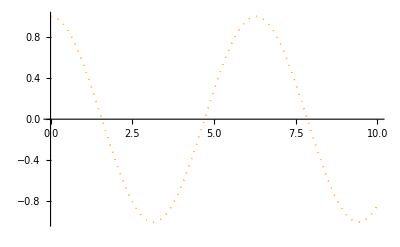

```mathematica
Plot[{exsol,sersol},{t,0,10},PlotRange->1,PlotStyle->{{Red,Dotted},{Yellow,Dotted}}]
```

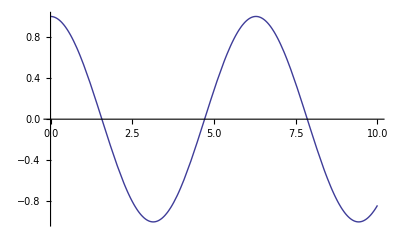

```mathematica
g1=Plot[exsol,{t,0,10}]
```

```mathematica
g2=Plot[sersol,{t,0,10},PlotRange->1]
```

-Graphics-

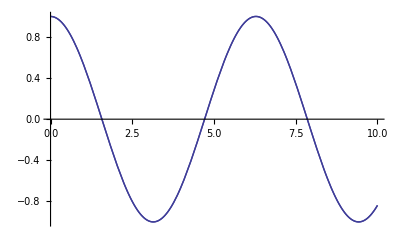

```mathematica
Show[g1,g2]
```